```mathematica
Clear[tEnd,tmax1,tmax2]
um=10^-6;
ms=10^-3;
MHz=10^6;
x=d(10 (t/tEnd)^3-15(t/tEnd)^4+ 6 (t/tEnd)^5);
v=D[x, t];
acc=D[(v), t];
pdacc=D[acc, t];
sol=Solve[pdacc==0,t];
tmax1=t/.sol[[1,1]];
tmax2=t/.sol[[2,1]];
accMax=acc/.t->tmax1;
FullSimplify[accMax]
```

(10 d)/(√3 tEnd^2)

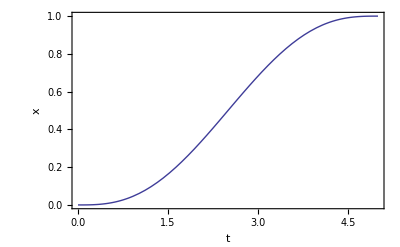

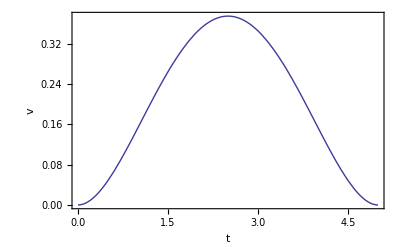

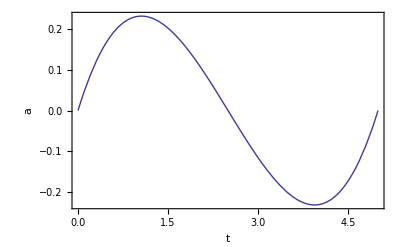

```mathematica
tEnd=5;
d=1;
Plot[x,{t,0,tEnd},Frame->True,FrameLabel->{"t","x"}]
Plot[v,{t,0,tEnd},Frame->True,FrameLabel->{"t","v"}]

Plot[acc,{t,0,tEnd},Frame->True,FrameLabel->{"t","a"}]
```

```mathematica
Clear[d,tEnd];
d=2.5um;
tEnd/ms/.Solve[accMax==(1um)/(ms)^2,tEnd][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

3.79918